## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW151226";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={};
mergerParams={};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

Part::partw: Part 5 of Missing[KeyAbsent,dalpha_3] does not exist.

```mathematica
samples
```

```mathematica
raw=Import[FileNameJoin[{baseDir,eventID,"GR"<>"_IMRP_posterior.csv"}]];
samples["GR"]=(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]](*spin2z*)};
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
onePlots=<||>;
twoPlots=<||>;
threePlots=<||>;
fourPlots=<||>;
fivePlots=<||>;
```

## Compute GR m1 and m2 PDF

```mathematica
p="GR"
m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];
```

GR

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 52060 + 镜像 52060

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_2"}; (*换参数改这里*)
CASE="p2";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.0316};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE],2];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],contourPoints[CASE],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.0316}，共 2 条

第一条前3点：{{12.7094,8.68945},{12.7633,8.65761},{12.7774,8.63552}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.097404

可信水平百分比：9.7404%

==========================

{dphi_2} 预处理完成，红线包含概率 prob = 0.097404

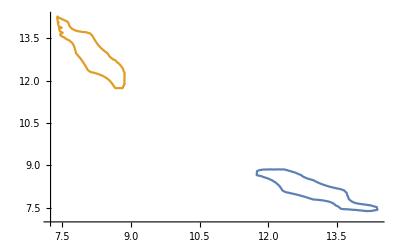

```mathematica
ListLinePlot[contourPoints[CASE]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_2}

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.42055, 0.57945}

GR 目标区间: {6.24799, 6.32996}

Param 目标区间: {5.951, 6.3645}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=4.44089×10^-16

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.67187×10^-16

Param下界: 点数=170 | Y>0点数=170 | 平均误差=4.02293×10^-16

Param上界: 点数=170 | Y>0点数=170 | 平均误差=8.82954×10^-16

{{3.1,11.2118},{3.2,11.5735},{3.3,11.9352},{3.4,12.2968},{3.5,12.6585}}

{{3.1,1.9615},{3.2,2.02478},{3.3,2.08805},{3.4,2.15133},{3.5,2.2146}}

chi1L取值：0.614549

chi2L取值：0.529968

=====================================================

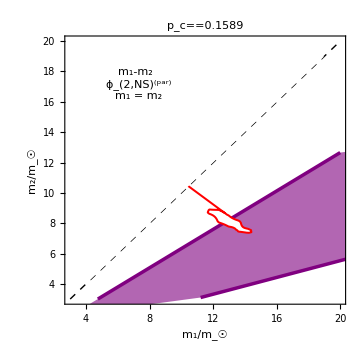

```mathematica
p={"dphi_2"}
probability=prob;
probability=0.1138;
probability=0.1589;
plots[CASE]=PlotMultiInversion[p,{probability},3,20,0.1,cm->True,cd->{1},cu->{0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->contourPoints[CASE]]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_4"}; (*换参数改这里*)
CASE="p4";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.03393};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],contourPoints[CASE],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.03393}，共 2 条

第一条前3点：{{12.7367,8.00005},{12.6988,8.01665},{12.6194,8.06877}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.0334253

可信水平百分比：3.34253%

==========================

{dphi_4} 预处理完成，红线包含概率 prob = 0.0334253

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

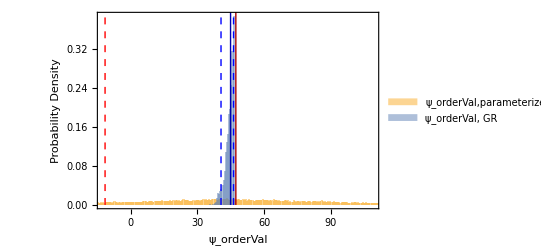

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_4}

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.483287, 0.516713}

GR 目标区间: {44.8136, 44.9611}

Param 目标区间: {45.7492, 48.7947}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=2.21522×10^-15

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.48796×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=8.48472×10^-15

Param上界: 点数=170 | Y>0点数=170 | 平均误差=2.54885

{{3.1,2.23219},{3.2,2.30419},{3.3,2.3762},{3.4,2.4482},{3.5,2.52021}}

{{3.1,3.1},{3.2,3.20001},{3.3,3.3},{3.4,3.4},{3.5,3.50001}}

chi1L取值：0.569676

chi2L取值：0.495363

=====================================================

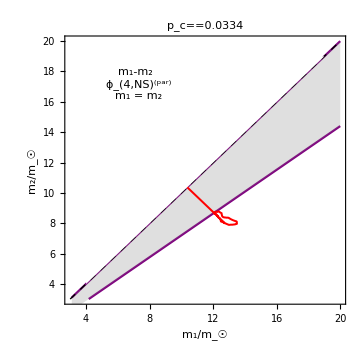

```mathematica
p={"dphi_4"}
probability=prob;
(*probability=0.07;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,20,0.1,cm->True,cd->{0},cu->{0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->contourPoints[CASE]]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_5l"}; (*换参数改这里*)
CASE="p5l";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.03262};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],contourPoints[CASE],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.03262}，共 2 条

第一条前3点：{{12.7094,7.95725},{12.7551,7.93728},{12.7857,7.92353}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.0669731

可信水平百分比：6.69731%

==========================

{dphi_5l} 预处理完成，红线包含概率 prob = 0.0669731

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

{dphi_5l}

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.466513, 0.533487}

GR 目标区间: {465.943, 466.24}

Param 目标区间: {436.543, 465.154}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=5.68434×10^-14

GR上界: 点数=170 | Y>0点数=170 | 平均误差=3.20998×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=28.2128

Param上界: 点数=170 | Y>0点数=170 | 平均误差=2.00624×10^-14

{{3.1,3.09994},{3.2,3.20007},{3.3,3.30006},{3.4,3.39996},{3.5,3.49998}}

{{3.1,2.27774},{3.2,2.35121},{3.3,2.42469},{3.4,2.49817},{3.5,2.57164}}

chi1L取值：0.556081

chi2L取值：0.549942

=====================================================

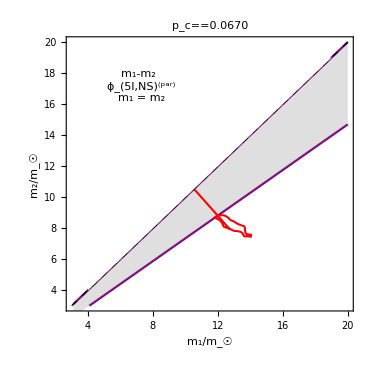

```mathematica
p={"dphi_5l"}
probability=prob;
(*probability=0.1;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,20,0.1,cm->True,cd->{0},cu->{0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiLNS},contourIndices->{1,2},m1m2region->contourPoints[CASE]]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_6"}; (*换参数改这里*)
CASE="p6";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.031};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],contourPoints[CASE],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.031}，共 2 条

第一条前3点：{{12.7094,8.72452},{12.7659,8.69113},{12.7995,8.67008}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.113841

可信水平百分比：11.3841%

==========================

{dphi_6} 预处理完成，红线包含概率 prob = 0.113841

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

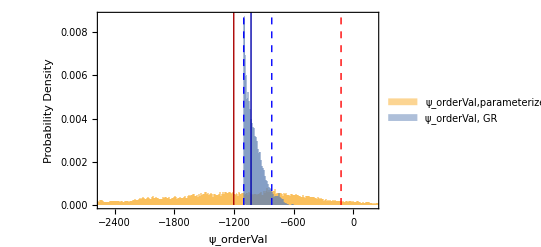

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_6}

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.44308, 0.55692}

GR 目标区间: {-1041.9, -1014.73}

Param 目标区间: {-1307.96, -1089.6}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=1.47124×10^-13

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.23049×10^-13

Param下界: 点数=170 | Y>0点数=170 | 平均误差=203.836

Param上界: 点数=170 | Y>0点数=170 | 平均误差=1.06999×10^-13

{{3.1,3.1},{3.2,3.19999},{3.3,3.29999},{3.4,3.4},{3.5,3.49999}}

{{3.1,2.37419},{3.2,2.45077},{3.3,2.52736},{3.4,2.60395},{3.5,2.68053}}

chi1L取值：0.531846

chi2L取值：0.440716

=====================================================

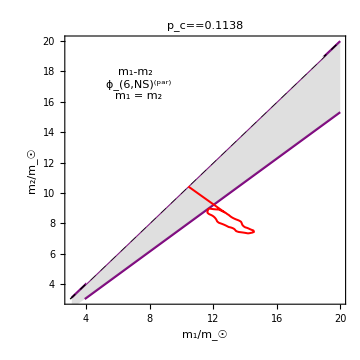

```mathematica
p={"dphi_6"}
probability=prob;
(*probability=0.1;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,20,0.1,cm->True,cd->{0},cu->{0},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->contourPoints[CASE]]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p={"dphi_7"}; (*换参数改这里*)
CASE="p7";

(*提取 0.005 密度对应的红线*)
contourPD[CASE]={0.02924};
{contourPlotObj[CASE],contourPoints[CASE]}=GetContourPlotAndPoints[m1m2PDF["GR"],m1PriorRange["GR"],m2PriorRange["GR"],contourPD[CASE]];

(*算出红线内部包含的真实后验概率 prob*)
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF["GR"],contourPoints[CASE],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.02924}，共 2 条

第一条前3点：{{14.1501,7.24968},{14.2166,7.24051},{14.2401,7.23933}}

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.158855

可信水平百分比：15.8855%

==========================

{dphi_7} 预处理完成，红线包含概率 prob = 0.158855

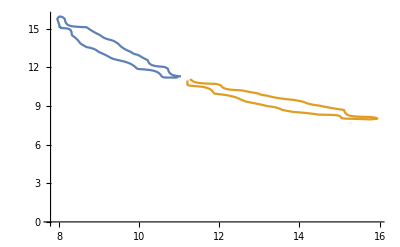

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

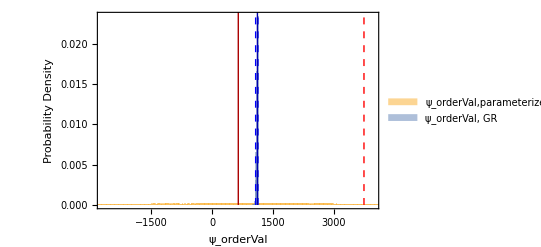

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

{dphi_7}

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.420573, 0.579427}

GR 目标区间: {1114.66, 1121.77}

Param 目标区间: {214.548, 1112.38}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=4.54747×10^-14

GR上界: 点数=170 | Y>0点数=170 | 平均误差=3.20998×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=738.967

Param上界: 点数=170 | Y>0点数=170 | 平均误差=1.41774×10^-13

{{3.1,329914.},{3.2,340556.},{3.3,351198.},{3.4,361840.},{3.5,372483.}}

{{3.1,6.29108},{3.2,6.49402},{3.3,6.69696},{3.4,6.8999},{3.5,7.10284}}

chi1L取值：0.552261

chi2L取值：0.528894

=====================================================

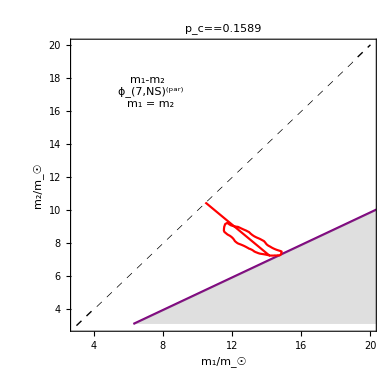

```mathematica
p={"dphi_7"}
probability=prob;
(*probability=0.1;*)
plots[CASE]=PlotMultiInversion[p,{probability},3,20,0.1,cm->True,cd->{1},cu->{1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS},contourIndices->{1,2},m1m2region->contourPoints[CASE]]
```

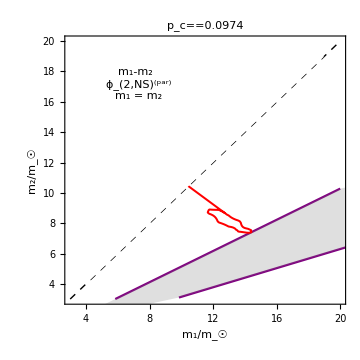
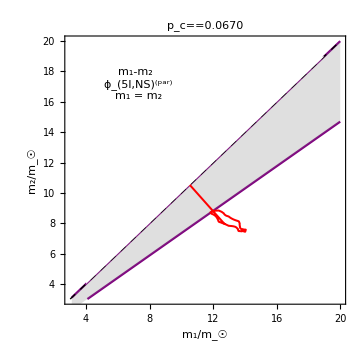
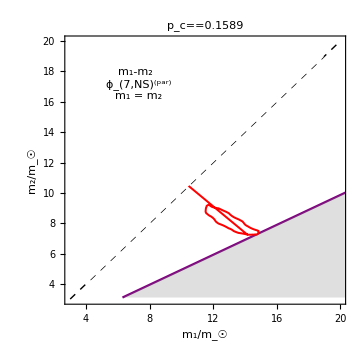
<|p2→-Graphics-,p4→-Graphics-,p5l→-Graphics-,p6→-Graphics-,p7→-Graphics-|>

```mathematica
plots
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.4513, 0.5487}

GR 目标区间: {6.26373, 6.31567}

Param 目标区间: {6.02695, 6.28428}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=1.41064×10^-16

GR上界: 点数=170 | Y>0点数=170 | 平均误差=3.86619×10^-16

Param下界: 点数=170 | Y>0点数=170 | 平均误差=7.94136×10^-16

Param上界: 点数=170 | Y>0点数=170 | 平均误差=2.24657×10^-16

{{3.1,9.84611},{3.2,10.1637},{3.3,10.4813},{3.4,10.799},{3.5,11.1166}}

{{3.1,1.59306},{3.2,1.64445},{3.3,1.69584},{3.4,1.74723},{3.5,1.79861}}

chi1L取值：0.614549

chi2L取值：0.529968

=====================================================

警告：参数 dphi_2 模式为 Points，但未提供有效 extremePointsList，已跳过。

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

概率区间: {0.4513, 0.5487}

GR 目标区间: {465.876, 466.312}

Param 目标区间: {429.653, 470.855}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=5.68434×10^-14

GR上界: 点数=170 | Y>0点数=170 | 平均误差=5.71778×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=35.1037

Param上界: 点数=170 | Y>0点数=170 | 平均误差=2.70842×10^-14

{{3.1,3.10008},{3.2,3.19994},{3.3,3.29999},{3.4,3.3999},{3.5,3.50008}}

{{3.1,12.3491},{3.2,12.7474},{3.3,13.1458},{3.4,13.5442},{3.5,13.9425}}

chi1L取值：0.556081

chi2L取值：0.549942

=====================================================

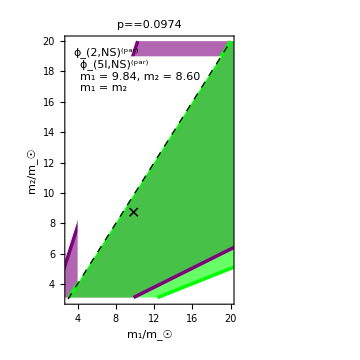

```mathematica
p={"dphi_2","dphi_5l"};
probability=prob;
probability=0.0974;
(*probability=0.2;*)
PlotMultiInversionWithMode[p,{probability,probability},3,20,0.1,cm->True,cd->{1,1},cu->{1,1},plotgr->False,projX->False,projY->False,funcName->{IMRPhenomDPhiNS,IMRPhenomDPhiLNS},contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[CASE][[1]],contourPoints[CASE][[2]],2]},
labelSymbol->Style["p",Italic],
mode->{"Points","Points"},
extremePointsList->{{},{m1m2Max}},extremePointsMarkerList->{"Cross","Cross"},extremePointsLegendList->{"",Row[{Subscript[Style["m",Italic],1]," = ",NumberForm[m1m2Max[[1]],{Infinity,2}],", ",(*两个值之间的分隔*)Subscript[Style["m",Italic],2]," = ",NumberForm[m1m2Max[[2]],{Infinity,2}]}]},
showVerificationStats->True]
```

# utils